```mathematica
(*Quiet[ DeleteDirectory[ "FitExamples", DeleteContents -> True ], DeleteDirectory::nodir ];*)
Quiet @ Unset @ PersistentSymbol[ "FITImport/FunctionalThresholdPower" ];
Quiet @ Unset @ PersistentSymbol[ "FITImport/MaxHeartRate" ];
Get @ FileNameJoin @ { NotebookDirectory[ ], "Definition.wl" };
TestReport @ FileNameJoin @ { NotebookDirectory[ ], "Tests.wlt" }
```

TestReportObject[…]

### Basic Examples

Import a fit file as a Dataset:

```mathematica
FITImport["ExampleData/BikeRide.fit"]
```

-Graphics-

Get a summary of the ride:

```mathematica
FITImport["ExampleData/BikeRide.fit","Session"]
```

-Graphics-

Get a TimeSeries of GPS coordinates:

```mathematica
FITImport["ExampleData/BikeRide.fit","GeoPosition"]
```

TemporalData[TimeSeries, <<1>>]

View a map of the route:

```mathematica
GeoGraphics[{Red,Thick,Line[Values[%]]}]
```

-Graphics-

Plot elevation over time:

```mathematica
DateListPlot[FITImport["ExampleData/BikeHillClimb.fit","Altitude"]]
```

-Graphics-

Visualize a workout:

```mathematica
FITImport["ExampleData/IndoorIntervals.fit","PowerZonePlot"]
```

-Graphics-

Visualize the power phase of pedal strokes in a bike ride:

```mathematica
FITImport["ExampleData/BikeLaps.fit","AveragePowerPhasePlot"]
```

-Graphics-

Get the critical power curve for a bike ride:

```mathematica
FITImport["ExampleData/BikeLaps.fit","CriticalPowerCurvePlot"]
```

-Graphics-

### Scope

Get information about devices used to generate the file:

```mathematica
FITImport["ExampleData/BikeHillClimb.fit","DeviceInformation"]
```

### Options

#### FunctionalThresholdPower

Some values are not available without specifying an FTP value:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","PowerZone"]
```

Missing[NotAvailable]

Specify an FTP when importing to get power zone data:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","PowerZone","FunctionalThresholdPower"->Quantity[250,"Watts"]]
```

TimeSeries[…]

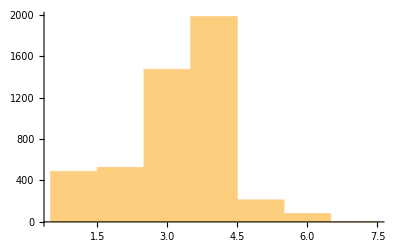

```mathematica
Histogram[Values[%]]
```

See how the distribution changes with different FTP values:

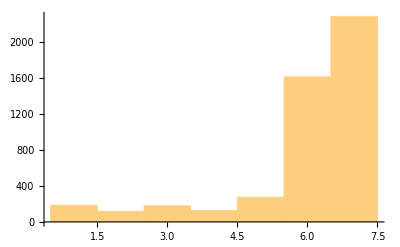
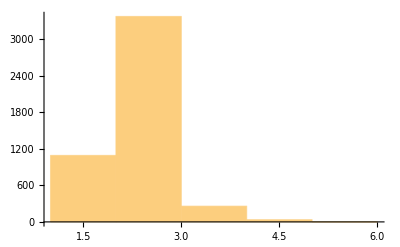
{-Graphics-,-Graphics-,-Graphics-}

```mathematica
Histogram[Values[FITImport["ExampleData/ZwiftRide.fit","PowerZone","FunctionalThresholdPower"->Quantity[#,"Watts"]]]]&/@{150,250,350}
```

Set the FTP persistently:

```mathematica
PersistentSymbol["FITImport/FunctionalThresholdPower"]=Quantity[250,"Watts"]
```

250 W

Specifying the FunctionalThresholdPower option is no longer necessary:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","PowerZone"]
```

TimeSeries[…]

Remove the stored value:

```mathematica
PersistentSymbol["FITImport/FunctionalThresholdPower"]=.
```

Some fit files have a stored FTP value:

```mathematica
FITImport["ExampleData/IndoorIntervals.fit","PowerZonePlot"]
```

-Graphics-

Override the value stored in the file:

```mathematica
FITImport["ExampleData/IndoorIntervals.fit","PowerZonePlot","FunctionalThresholdPower"->Quantity[400,"Watts"]]
```

-Graphics-

Other files may not store this information:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","PowerZonePlot"]
```

FITImport::NoFTPValue: No functional threshold power specified.

-Graphics-

Set the FTP manually:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","PowerZonePlot","FunctionalThresholdPower"->Quantity[250,"Watts"]]
```

-Graphics-

#### MaxHeartRate

Some values are not available without specifying a maximum heart rate:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","HeartRateZone"]
```

Missing[NotAvailable]

Specify a max heart rate when importing to get HR zone data:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","HeartRateZone","MaxHeartRate"->190]
```

TimeSeries[…]

```mathematica
Histogram[Values[%]]
```

-Graphics-

Set the max heart rate persistently:

```mathematica
PersistentSymbol["FITImport/MaxHeartRate"]=Quantity[190,"BPM"]
```

190 beats/min

Specifying the MaxHeartRate option is no longer necessary:

```mathematica
FITImport["ExampleData/ZwiftRide.fit","HeartRateZone"]
```

TimeSeries[…]

Remove the stored value:

```mathematica
PersistentSymbol["FITImport/MaxHeartRate"]=.
```

#### UnitSystem

By default, units are determined by the current value of $UnitSystem:

```mathematica
$UnitSystem
```

Imperial

```mathematica
FITImport["ExampleData/BikeHillClimb.fit","Altitude"]["LastValue"]
```

2591.21 ft

Override the default unit system:

```mathematica
FITImport["ExampleData/BikeHillClimb.fit","Altitude",UnitSystem->"Metric"]["LastValue"]
```

789.8 m

### Applications

### Properties and Relations

Get the number of each message type in a fit file:

```mathematica
FITImport["ExampleData/BikeRide.fit","MessageCounts"]
```

<|FileID→1,FileCreator→1,Event→264,DeviceInformation→19,DeviceSettings→1,UserProfile→1,Sport→1,ZonesTarget→1,TrainingFile→1,Record→11376,HeartRateVariability→11479,SegmentLap→1,Lap→2,Session→1,Activity→1|>

Get information about the fit messages contained in a file:

```mathematica
FITImport["ExampleData/BikeRide.fit","MessageInformation"]//Dataset
```

Check for message types that are not currently importable:

```mathematica
Select[%,!#["Supported"]&]
```

### Possible Issues

### Neat Examples

Animate a bike ride:

```mathematica
alt=Values[FITImport["ExampleData/BikeHillClimb.fit","Altitude"]][[;;;;10]];
pos=Values[FITImport["ExampleData/BikeHillClimb.fit","GeoPosition"]][[;;;;10]];
bounds=GeoBoundingBox[pos];
Animate[{
GeoGraphics[{Thick,Red,Line[Take[pos,n]]},GeoRange->bounds],
Show[ListLinePlot[alt],ListLinePlot[Take[alt,n],Filling->Bottom]]
},{n,1,Length[pos],1},DefaultDuration->30]
```

-Graphics-

Plot all the values found in a fit file:

```mathematica
Short[ts=KeyDrop[FITImport["ExampleData/BikeHillClimb.fit",All],{"Timestamp","GeoPosition","MessageType"}]]
```

<|Distance→TimeSeries[…],Altitude→TimeSeries[…],«14»,RespirationRate→TimeSeries[…]|>

```mathematica
Multicolumn[KeyValueMap[DateListPlot[TimeSeriesResample[#2,30],PlotLabel->#1]&,ts],3]
```

-Graphics-

Animate a Zwift ride:

```mathematica
pos=Reverse/@Values[FITImport["ExampleData/ZwiftRide.fit","GeoPosition"]][[All,1]];
watopia=ImageResize[First@Import["https://zwiftinsider.com/wp-content/uploads/2022/09/Watopia-2.15.pdf"],500];
Animate[
ImageCompose[Show[watopia,ImageSize->500],Graphics[{Thickness[.01],Yellow,Line[Take[pos,n]],Green,Disk[pos[[n]],0.0005]},],Scaled[{0.2966,0.3302}]],
{n,1,Length[pos],1},
DefaultDuration->30
]
```

-Graphics-